```mathematica
<<MagneticTB`
```

### Kagomi lattice

```mathematica
kagomi=initSSG@<|
"lattice"->{{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}},
"lattpar"->{a->1,c->3},
"wyckoffposition"->Association["C"->Association[
"FractionalCoordinates"->{1/2,0,0},
"MagnetizationDirection"->{1,-1,0},
(*"MagnetizationDirection"->{0,0,0},*)
"BasisFunction"->{(*"x","y"*){0,1},{1,0}}
]
],
"symminformation"->Association[
"6z+3z"-><|"space"->{{{1,-1,0},{1,0,0},{0,0,1}},{0,0,0}},"spin"->{{{0,-1,0},{1,-1,0},{0,0,1}},0}|>,
"2x+2x"-><|"space"->{{{1,0,0},{1,-1,0},{0,0,-1}},{0,0,0}},"spin"->{{{1,0,0},{1,-1,0},{0,0,-1}},0}|>,
"P+E"-><|"space"->{{{-1,0,0},{0,-1,0},{0,0,-1}},{0,0,0}},"spin"->{{{1,0,0},{0,1,0},{0,0,1}},0}|>(*,
"E+T"-><|"space"->{{{1,0,0},{0,1,0},{0,0,1}},{0,0,0}},"spin"->{{{1,0,0},{0,1,0},{0,0,1}},1}|>*)
]|>;
```

```mathematica
ham0=Sum[symhamSSG[i,kagomi],{i,2}];MatrixForm[ham0]
```

params:{e1,e2}

params:{t1,t2,t3,t4}

(e2 | e1-(ⅈ e1)/(√3) | ⅇ^(-(ⅈ ky)/2) (ⅈ t1+t4)+ⅇ^((ⅈ ky)/2) (ⅈ t1+t4) | ⅇ^(-(ⅈ ky)/2) (t3+(ⅈ t3)/(√3))+ⅇ^((ⅈ ky)/2) (t3+(ⅈ t3)/(√3)) | ⅇ^(ⅈ (-kx/2-ky/2)) (-ⅈ t1+t4)+ⅇ^(ⅈ (kx/2+ky/2)) (-ⅈ t1+t4) | -(2 ⅈ ⅇ^(ⅈ (-kx/2-ky/2)) t2)/(√3)-(2 ⅈ ⅇ^(ⅈ (kx/2+ky/2)) t2)/(√3)
e1+(ⅈ e1)/(√3) | e2 | ⅇ^(-(ⅈ ky)/2) (t2-(ⅈ t2)/(√3))+ⅇ^((ⅈ ky)/2) (t2-(ⅈ t2)/(√3)) | ⅇ^(-(ⅈ ky)/2) (-ⅈ t1+t4)+ⅇ^((ⅈ ky)/2) (-ⅈ t1+t4) | (2 ⅈ ⅇ^(ⅈ (-kx/2-ky/2)) t3)/(√3)+(2 ⅈ ⅇ^(ⅈ (kx/2+ky/2)) t3)/(√3) | ⅇ^(ⅈ (-kx/2-ky/2)) (ⅈ t1+t4)+ⅇ^(ⅈ (kx/2+ky/2)) (ⅈ t1+t4)
ⅇ^(-(ⅈ ky)/2) (-ⅈ t1+t4)+ⅇ^((ⅈ ky)/2) (-ⅈ t1+t4) | ⅇ^(-(ⅈ ky)/2) (t2+(ⅈ t2)/(√3))+ⅇ^((ⅈ ky)/2) (t2+(ⅈ t2)/(√3)) | e2 | (2 ⅈ e1)/(√3) | ⅇ^(-(ⅈ kx)/2) (ⅈ t1+t4)+ⅇ^((ⅈ kx)/2) (ⅈ t1+t4) | ⅇ^(-(ⅈ kx)/2) (-t3+(ⅈ t3)/(√3))+ⅇ^((ⅈ kx)/2) (-t3+(ⅈ t3)/(√3))
ⅇ^(-(ⅈ ky)/2) (t3-(ⅈ t3)/(√3))+ⅇ^((ⅈ ky)/2) (t3-(ⅈ t3)/(√3)) | ⅇ^(-(ⅈ ky)/2) (ⅈ t1+t4)+ⅇ^((ⅈ ky)/2) (ⅈ t1+t4) | -(2 ⅈ e1)/(√3) | e2 | ⅇ^(-(ⅈ kx)/2) (-t2-(ⅈ t2)/(√3))+ⅇ^((ⅈ kx)/2) (-t2-(ⅈ t2)/(√3)) | ⅇ^(-(ⅈ kx)/2) (-ⅈ t1+t4)+ⅇ^((ⅈ kx)/2) (-ⅈ t1+t4)
ⅇ^(ⅈ (-kx/2-ky/2)) (ⅈ t1+t4)+ⅇ^(ⅈ (kx/2+ky/2)) (ⅈ t1+t4) | -(2 ⅈ ⅇ^(ⅈ (-kx/2-ky/2)) t3)/(√3)-(2 ⅈ ⅇ^(ⅈ (kx/2+ky/2)) t3)/(√3) | ⅇ^(-(ⅈ kx)/2) (-ⅈ t1+t4)+ⅇ^((ⅈ kx)/2) (-ⅈ t1+t4) | ⅇ^(-(ⅈ kx)/2) (-t2+(ⅈ t2)/(√3))+ⅇ^((ⅈ kx)/2) (-t2+(ⅈ t2)/(√3)) | e2 | -e1-(ⅈ e1)/(√3)
(2 ⅈ ⅇ^(ⅈ (-kx/2-ky/2)) t2)/(√3)+(2 ⅈ ⅇ^(ⅈ (kx/2+ky/2)) t2)/(√3) | ⅇ^(ⅈ (-kx/2-ky/2)) (-ⅈ t1+t4)+ⅇ^(ⅈ (kx/2+ky/2)) (-ⅈ t1+t4) | ⅇ^(-(ⅈ kx)/2) (-t3-(ⅈ t3)/(√3))+ⅇ^((ⅈ kx)/2) (-t3-(ⅈ t3)/(√3)) | ⅇ^(-(ⅈ kx)/2) (ⅈ t1+t4)+ⅇ^((ⅈ kx)/2) (ⅈ t1+t4) | -e1+(ⅈ e1)/(√3) | e2)

```mathematica
path = {
{{{0,0,0},{1/3,1/3,0}},{"G","K"}},
{{{1/3,1/3,0},{1/2,0,0}},{"K","M"}},
{{{1/2,0,0},{0,0,0}},{"M","G"}}
};
bandManipulate[path,50,ham0]
```

Number of params:6

params:{e1,e2,t1,t2,t3,t4}

{e1→-0.498,e2→0.258,t1→0,t2→0,t3→0.194,t4→0}

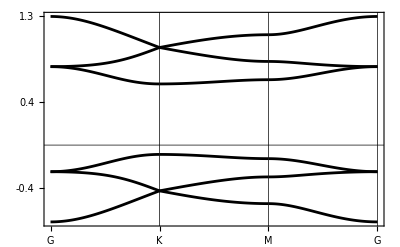

```mathematica
bandplot[path,200,ham0,{e1->-0.498,e2->0.258,t1->0,t2->0,t3->0.19399999999999995,t4->0}]
```